## init

Set the library’s directory first!

```mathematica
directory=NotebookDirectory[]
```

/home/tchr/Projects/Mathematica-MSE/library/docs/

```mathematica
directory="/home/tchr/Projects/Mathematica-MSE/library/";
(* For windows use the following format instead*)
(*directory="E:\\BITBUCKET\\MSE\\library\\";*)
```

```mathematica
Get["mse.m",Path->directory]
```

{45132168,36709256,1}

## Import precomputed data

Set the data’s directory preferably in the variable ‘filename’.

```mathematica
filename=directory<>"import/"<>"round1m1-1.xls.pre.dat"
```

/home/tchr/Projects/Mathematica-MSE/library/import/round1m1-1.xls.pre.dat

```mathematica
(*filename=directory<>"import/"<>"round1m2-1.xls.pre.dat"*)
```

```mathematica
?import
```

{noM,no,u,noAttr}=import[filename,"stream"] to load an upstream.

{noM,no,d,noAttr}=import[filename,"stream"] to load a downstream.

imports a file .xls or .xlsx or a tab delimited file .dat that includes data corresponding to an upstream (u) or downstream (d).

Datafiles consist of rows in the form {noM,no,attr1,attr2,...,attrn,noAttr}.

In the case of .xls or .xlsx files multiple sheets are joined - for example if each market resides in its own excel sheet.

__________________________________________________________________________________________________

{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}=import[filename_,"precomp",printflag_:False]

imports a file .xls or .xlsx or a tab delimited file .dat that includes precomputed matched data (distances between same attributes are already computed).

Datafiles consists of rows in the form {m,u,d,u1,d1,u2,d2,...,un,dn,matched (0 or 1)}.

In the case of .xls or .xlsx files multiple sheets are joined - for example if each market resides in its own excel sheet.

Load the data in variables with meaningful names

```mathematica
{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}=import[filename,"precomp"];
```

## Routines (calculate payoff matrix, inequalities members, dataArray)

```mathematica
?CpayoffMatrix
```

payoffMatrix=CpayoffMatrix[payoff(or payoffDM),noM_:noM,noU_:noU,noD_:noD,parallel_:True] calculates and assigns the payoffMatrix.
 
In case of separated streams payoff is used and in the case of precomputed data payoffDM is used.

```mathematica
??payoffDM
```

payoffDM[m,i,j] returns the payoff of i-upstream and j-upstream in the m-market.

It is used in the case of precomputed data. It is assumed that noAttr and distanceMatrices have been already assigned.

payoffDM[m_,i_,j_]:=Prepend[Cx[noAttr-1],1].distanceMatrices⟦m,i,j⟧

```mathematica
payoffMatrix=CpayoffMatrix[payoffDM,noM,noU,noD];
```

```mathematica
?Cineqmembers
```

Cineqmembers[mate] generates all the members required to form the inequalities for many to many relationships defined by the mate. The produced list of lists of triples define also the way inequalities are formed. At this time there is only one way we have to create inequalities. CAUTION: ineqmembers is the largest object so it consumes a lot of memory. This is why we use MSEresources="Memory" when it is needed. Be carefull because then ineqmembers are erased after used for the dataArray calculation (only in the memory model).
Cineqmembers[mate,"2"] applies the second method....

Cineqmembers[mate] generates all the members required to form the inequalities for many to many relationships defined by the mate. The produced list of lists of triples define also the way inequalities are formed. At this time there is only one way we have to create inequalities. CAUTION: ineqmembers is the largest object so it consumes a lot of memory. This is why we use MSEresources="Memory" when it is needed. Be carefull because then ineqmembers are erased after used for the dataArray calculation (only in the memory model).\nCineqmembers[mate,"2"] applies the second method....\n

```mathematica
ineqmembers=Cineqmembers[mate];
```

```mathematica
?CdataArray
```

CdataArray[payoffMatrix,xlist,printflag] creates the dataArray. It works either using the "Speed" model or the "Memory" model. It uses ineqmembers and Cinequalities internally and for the memory model it erases ineqmembers after use.

```mathematica
dataArray=CdataArray[payoffMatrix,Cx[noAttr-1]];
```

## Maximization

permuteinvariant variable role ...

```mathematica
permuteinvariant=True;
```

The default DifferentialEvolution parameters:

option name | default value |  
"CrossProbability" | 0.5 | probability that a gene is taken from x_i
"InitialPoints" | Automatic | set of initial points 
"PenaltyFunction" | Automatic | function applied to constraints to penalize invalid points
"PostProcess" | Automatic | whether to post-process using local search methods 
"RandomSeed" | 0 | starting value for the random number generator
"ScalingFactor" | 0.6 | scale applied to the difference vector in creating a mate 
"SearchPoints" | Automatic | size of the population used for evolution 
"Tolerance" | 0.001 | tolerance for accepting constraint violations

```mathematica
?maximize
```

maximize[dataArray_,noAttr_,method_:"DifferentialEvolution",permuteinvariant_:False,printflag_:False] is MSE specific and uses the optimize method. It uses objective function (that counts the number of satisfied inequalities).

```mathematica
method1={"DifferentialEvolution","CrossProbability"->0.5,"InitialPoints"->Automatic,"PenaltyFunction"->Automatic,"PostProcess"->Automatic,"RandomSeed"->0,"ScalingFactor"->0.6,"SearchPoints"->Automatic,"Tolerance"->0.001};
sol1=maximize[dataArray,noAttr,method1,permuteinvariant,True];
```

order={2,1}  reverse order={3.18803,2.22377}

Method {DifferentialEvolution, CrossProbability -> 0.5, InitialPoints -> Automatic, PenaltyFunction -> Automatic, PostProcess -> Automatic, RandomSeed -> 0, ScalingFactor -> 0.6, SearchPoints -> Automatic, Tolerance -> 0.001}

Completed : {29961.,{Distance2→3.18803,Distance3→2.22377}}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1199 | 1188 | 1210 | 1205 | 1200 | 1197 | 1207 | 1194 | 1199 | 1189 | 1203 | 1198 | 1199 | 1210 | 1196 | 1204 | 1198 | 1194 | 1189 | 1197 | 1188 | 1206 | 1195 | 1203 | 1193
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 99 | 98 | 98 | 98 | 99 | 97 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 98 | 97 | 97 | 98 | 97 | 98 | 98 | 98 | 97

```mathematica
?pso
```

pso[objFun_,nparts_Integer,bndLo_List,bndUp_List,niter_Integer:100,r_Integer:1]
nparts: the number of particles
bndLo: a list of the lower bounds, one for each dimension
bndUp: a list of the upper bounds, one for each dimension
niter: Number of iterations
r: length of the toroidal neighbour scheme e.g. r=1 gives (i-1 mod nparts, i, i+1 mod nparts) as the neighbours of particle i

```mathematica
method2={"ParticleSwarmOptimization","nparts"->32,"bndLo"->-10,"bndUp"->10,"niter"->200,"r"->1,"RandomSeed"->0};
sol2=maximize[dataArray,noAttr,method2,permuteinvariant,True];
```

order={2,1}  reverse order={3.64691,2.68339}

Method {ParticleSwarmOptimization, nparts -> 32, bndLo -> -10, bndUp -> 10, niter -> 200, r -> 1, RandomSeed -> 0}

Completed : {29965,{Distance2→3.64691,Distance3→2.68339}}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1201 | 1191 | 1206 | 1205 | 1199 | 1198 | 1207 | 1196 | 1198 | 1191 | 1203 | 1199 | 1197 | 1209 | 1196 | 1205 | 1194 | 1195 | 1190 | 1199 | 1186 | 1205 | 1198 | 1204 | 1193
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 98 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 97 | 98 | 97 | 98 | 98 | 98 | 97

## Confidence Intervals

```mathematica
sol=sol1;method=method1;
(*sol=sol2;method=method2;*)
```

```mathematica
ssSize=3;numSubsamples=50;alpha=0.05;
```

Starting pointIdentified process where alpha = 0.05

{4, 18, 20} {10, 14, 23} {6, 11, 18} {14, 19, 24} {5, 7, 23} {5, 9, 18} {4, 19, 22} {5, 17, 23} {2, 12, 24} {14, 15, 24}
Iterations completed:10
 {5, 13, 20} {9, 15, 24} {3, 5, 23} {11, 14, 17} {1, 5, 17} {2, 15, 25} {3, 14, 20} {4, 14, 16} {4, 8, 21} {5, 10, 21}
Iterations completed:20
 {3, 6, 22} {1, 7, 15} {9, 11, 19} {1, 3, 25} {2, 11, 14} {4, 5, 23} {10, 16, 20} {5, 8, 13} {2, 10, 15} {2, 19, 23}
Iterations completed:30
 {9, 20, 24} {1, 13, 21} {6, 18, 21} {2, 22, 25} {2, 3, 11} {8, 17, 22} {11, 19, 20} {18, 20, 24} {12, 13, 14} {2, 17, 20}
Iterations completed:40
 {7, 11, 16} {1, 3, 16} {2, 7, 12} {4, 16, 24} {3, 7, 24} {7, 17, 23} {18, 20, 22} {1, 14, 18} {7, 14, 24} {8, 13, 17}
Iterations completed:50

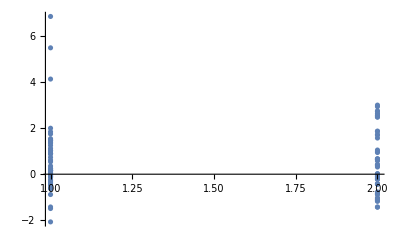
{32.4128,{{{{Symmetric case,{Distance2→{1.7754,4.60066},Distance3→{1.28489,3.16265}}},{Asymmetric case,{Distance2→{1.31168,3.69769},Distance3→{1.22111,2.7118}}}},{{1.12377,2.93178},{0.355918,1.04904},{0.237429,0.312546},{1.39069,-1.1774},{0.610695,1.56992},{1.24987,2.7453},{-2.07073,-1.039},{0.0268153,1.70537},{-0.60977,-1.42836},{1.45638,-0.846891},{1.46368,2.99964},{1.84103,-0.86256},{0.242902,-0.180578},{-0.2607,-0.0827866},{0.146192,1.71186},{-0.321707,-1.11994},{-0.083839,-0.0346359},{-0.1287,0.675002},{0.151682,-0.111352},{5.48648,0.940712},{-0.356819,-0.42704},{0.899683,1.85478},{-0.491326,-0.230117},{-1.42245,-1.03283},{1.99657,0.372449},{0.163816,0.983564},{1.02351,2.47603},{0.879305,0.416347},{6.84841,0.578446},{0.537859,0.652177},{1.34876,2.48994},{-0.0574272,-0.43399},{4.13057,-0.207907},{-1.49024,-1.10163},{-0.882507,-0.873011},{-0.422583,0.0104548},{1.74585,2.72943},{1.54122,2.5691},{0.181063,0.0253737},{0.733438,2.6362},{1.01966,0.643077},{-0.0844444,-0.413815},{-0.626745,-1.427},{0.893687,0.654948},{-0.121401,-0.771029},{-0.0150752,1.87232},{-0.2567,0.406811},{1.49344,2.54281},{0.0694083,-1.15305},{0.152533,-0.127103}}},-Graphics-}}

```mathematica
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,permuteinvariant,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10];
{pointIdentified,
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming
```